```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[8],Join[Table[{i,i-1},{i,Range[2,8,1]}],Table[{i,i+1},{i,Range[1,8,1]}]]->t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[8],Table[{2n,2n},{n,Range[1,4,1]}]->t]
```

```mathematica
T2[t_]:=T2[t]=ReplacePart[0*IdentityMatrix[8],Table[{2n-1,2n-1},{n,Range[1,4,1]}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],A:=Inverse[β[ω,0.001,1,0]],B:=Inverse[β[ω,0.001,1,0]],T1:=T1[1],T2:=T2[1]},Do[J=Inverse[IdentityMatrix[8]-A.T1.Inverse[IdentityMatrix[8]-B.T2.J.T2].B.T1].A,8000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[8]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[8]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[8]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[8]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

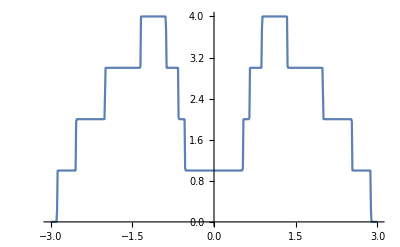
{429.905,-Graphics-}

```mathematica
Timing[ListLinePlot[Table[{ω,Print["Working on energy = "<>ToString[ω]<>"...."];Abs[tr[ω,0.001,1,0]]},{ω,Range[-3,3,0.01]}]]]
```